# Caminatas cuánticas

## Importando cosas

```mathematica
Get["/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/DTQW.wl"]
```

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

## Inicializaciones

```mathematica
InitializeDTQW[2,201]
```

```mathematica
MakeCoin[1/2,0,0];
```

```mathematica
MakeShift[];
```

```mathematica
MakeUnitary[];
```

## Caminata

```mathematica
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{ⅈ/(√2),1,0}}]

```mathematica
psif=DTQW2[psi0,100];
```

```mathematica
rho=MatrixPartialTrace[psif.psif†,1,{2,201}];
```

```mathematica
probs=Abs@Diagonal[rho];
```

```mathematica
Total[probs]
```

1.

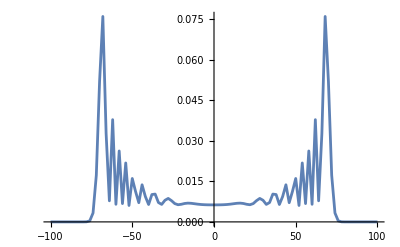

```mathematica
ListLinePlot[{Range[-100,100,2],probs[[;;;;2]]}ᵀ,
PlotRange->All
]
```

## Con decoherencia

```mathematica
rhofwd=DTQW2wDecoherence[psi0,0.99,100];
```

```mathematica
probswd=Abs@Diagonal@MatrixPartialTrace[rhofwd,1,{2,201}];
```

```mathematica
Total[probswd]
```

1.

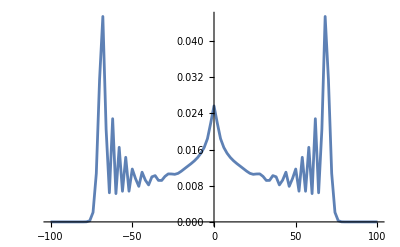

```mathematica
ListLinePlot[{Range[-100,100,2],probswd[[;;;;2]]}ᵀ,
PlotRange->All
]
```